# PLAPT: Protein - Ligand Binding Affinity Prediction Using Pretrained Transformer Models

Tyler Rose, Tony Shen, Ryan Tong

This study introduces the Protein-Ligand Affinity Prediction Transformer (PLAPT) model, an innovative machine learning approach to predict protein-ligand binding affinities with high accuracy, leveraging the strengths of pretrained transformer models. By employing ProtBERT and ChemBERTa for encoding protein and ligand sequences, respectively, we trained a two-branch dense neural network that effectively fuses these encodings to estimate binding affinity values. The model was trained on an extensive dataset amalgamated from sources such as BindingDB, PDBbind-cn, BioLIP, and BindingMOAD, consisting of 100,000 data points processed and curated in Python. The PLAPT model not only achieves a high Pearson correlation coefficient of 0.795, but also exhibits negligible overfitting, a notable improvement over existing state-of-the-art models.  This advancement shows the  potential for using pre-trained encoders for highly effective  predictive bioinformatics models, trained at a very low cost.

## Introduction

The quantification of protein-ligand binding affinities is fundamental to the process of drug design and development. Accurate predictions of such affinities can significantly speed up the identification of therapeutic candidates, thus expediating the drug discovery pipeline. While experimental methods provide the most reliable measures of binding affinities, their high costs, substantial time requirements, and limited throughput have prompted a shift towards computational approaches. In recent years, advancements in machine learning (ML) have opened new avenues for high-throughput in silico prediction of protein-ligand binding affinities. This paper introduces a novel method, Protein Ligand Affinity using Pretrained Transformers (PLAPT), which harnesses the representational capabilities of pretrained transformer models, namely ProtBERT for proteins and ChemBERTa for ligands, to predict binding affinity values through a two-branch dense neural network.

### Background and Related Work

#### Computational Methods for Predicting Protein-Ligand Binding Affinity

Various computational methods have been developed for protein - ligand binding affinity prediction . Traditional approaches, such as molecular docking, employ heuristic algorithms to simulate the interaction between proteins and small molecules, generating plausible bound conformations and estimating their affinities . Molecular dynamics simulations provide a more nuanced perspective by considering the dynamic behavior of protein - ligand complexes over time, albeit with significant computational cost . Free energy perturbation methods offer a thermodynamically rigorous calculation of binding affinities but are hindered by their demand for extensive computational resources .

#### Machine Learning for Protein-Ligand Binding Affinity Prediction

Prior to the adoption of deep learning techniques, several traditional ML algorithms have been used . Models such as Random Forests and Support Vector Machines capitalized on handcrafted features derived from protein and ligand properties to make predictions . Despite their successes, these methods were frequently limited by the quality and completeness of the feature sets used . 

The advent of transformer models, such as BERT (Bidirectional Encoder Representations from Transformers), has revolutionized the field of natural language processing . ProtBERT and ChemBERTa have adapted this architecture to encode, respectively, the amino acid sequences of proteins and the molecular sequences of ligands . These models capture complex relationships within the sequence data by pretraining on vast corpuses, enabling nuanced and context - aware embeddings that serve as a rich source of features for downstream tasks .

#### Examining Other ML Approaches

Other ML approaches have sought to advance protein-ligand binding affinity prediction by focusing on various facets of the protein-ligand interaction. CAPLA utilizes a deep learning architecture with a cross-attention mechanism to capture mutual effects, integrating features from both protein and ligand sequences. It emphasizes structure complementarity by learning from sequence-level information and employs interpretability techniques to identify key residues influencing binding affinity. DLSSAffinity, alternatively, combines the use of local structural information and global full-length protein sequences to account for both short-range direct and long-range indirect interactions, demonstrating strong performance against benchmark datasets. Similarly, OnionNet deploys a deep convolutional neural network, leveraging rotation-free element-pair contacts at varying distances to encapsulate both local and nonlocal interactions, thus aiming to enhance predictive robustness. These methods have each demonstrated improvements over existing baseline approaches in binding affinity prediction. PLAPT’s approach, however, integrates the generalizing strengths of ProtBERT and ChemBERTa to produce high quality encodings.  The representations obtained from these pretrained transformer models will lead to further enhanced accuracy in affinity prediction when used to train a two-branch dense neural network.

## Methodology

In our methodology, we present a comprehensive approach to predicting the interaction affinity between proteins and ligands. Initially, we source encoded protein-ligand pairs with their corresponding affinity values from a dataset generated in python using ProtBERT and ChemBERT. We then prepare this data for training the neural network by concatenating embeddings and dividing the set into subsets for training and evaluation purposes.

For developing the model, we use a dual-branch neural network designed to process the embeddings of proteins and molecules. It is then trained on the GPU. For testing and usage, it is unnecessary to train a network and therefore we offer the option to import a pre-trained model to bypass the training process.

For model inference, we developed tokenizers for both protein sequences and molecular SMILES data. After importing the encoding models, we convert the normalized prediction outputs into actual affinity values. Our end-to-end inference mechanism seamlessly takes string inputs of proteins and molecule SMILES and returns their binding affinity, streamlining prediction.

#### Diagram of PLAPT

## Data

### Import Embeddings

import the raw data

```mathematica
dataRaw = Import[FileNameJoin[{$UserDocumentsDirectory, "WELP-PLAPT", "data", "tensor_dataset100k.json"}]];
dataRaw = Association @@ # & /@ dataRaw;
```

```mathematica
data = Dataset[dataRaw];
```

```mathematica
Length@data
```

100000

```mathematica
data[[1]]
```

### Prepare Data For Training

```mathematica
data = (Append[#, "concat_embeddings" -> Join[#["prot_embeddings"], #["mol_embeddings"]]]) & /@ data;
```

```mathematica
data[[1]]
```

```mathematica
train=RandomSample[data,Length[data]*0.9];
Length@train
```

90000

```mathematica
test=Complement[data,train];
Length@test
```

10000

```mathematica
trainInputs=Normal@train[All,"concat_embeddings"];
trainOutputs=Normal@train[All,"affinity"];
```

```mathematica
testInputs=Normal@test[All,"concat_embeddings"];
testOutputs=Normal@test[All,"affinity"];
```

## Training

### Initialize Neural Network

```mathematica
net = NetGraph[
   {"ProtOnly" -> PartLayer[1 ;; 1024],
    "MolOnly" -> PartLayer[1025 ;; 1792],
    "ProtLinear" -> LinearLayer[512], "ProtRamp" -> Ramp,
    "MolLinear" -> LinearLayer[512], "MolRamp" -> Ramp,
    "Combined" -> (*ThreadingLayer[Plus]*)CatenateLayer[], "Normalize" -> BatchNormalizationLayer[],
    "Linear1" -> LinearLayer[512], "Ramp1" -> Ramp, "Dropout1" -> DropoutLayer[0.2],
    "Linear2" -> LinearLayer[64], "Ramp2" -> Ramp,
    "FinalLinear" -> LinearLayer[1]},
   {NetPort["Input"] -> "ProtOnly" -> "ProtLinear" -> "ProtRamp",
    NetPort["Input"] -> "MolOnly" -> "MolLinear" -> "MolRamp", 
    {"ProtRamp", "MolRamp"} -> "Combined" -> "Normalize" -> "Linear1" -> "Ramp1" -> "Dropout1" ->
    "Linear2" -> "Ramp2" -> "FinalLinear" -> NetPort["Output"]},
    "Input" -> 1792, "Output" -> "Scalar"
   ];
net = NetInitialize[net]
```

NetGraph[<>]

### Train Neural Network

```mathematica
TrainingProtocol[net_,trainInputs_,trainOutputs_,testInputs_,testOutputs_]:=NetTrain[
	net,
	<|"Input"->trainInputs,"Output"->trainOutputs|>,
	LossFunction->MeanSquaredLossLayer[],
	BatchSize->32,
	MaxTrainingRounds->60,
	ValidationSet-><|"Input"->testInputs,"Output"->testOutputs|>,
	TrainingProgressReporting->"Panel",
	WorkingPrecision->"Real32",
	TargetDevice->"GPU"
]
```

#### Training Neural Network

```mathematica
trainedNet=TrainingProtocol[net,trainInputs,trainOutputs,testInputs,testOutputs]
```

NetGraph[<>]

```mathematica
Mean[Power[testOutputs-trainedNet[testInputs],2]]
```

0.619095

#### Export trained model

```mathematica
Export[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","affinity_predictor.onnx"}],net]
```

C:\Users\tatwo\Documents\WELP-PLAPT\models\affinity_predictor.onnx

```mathematica
plapt=trainedNet
```

## Import the Pre-Trained PLAPT Model (Optional)

```mathematica
plapt=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","affinity_predictor.onnx"}]]
```

NetGraph[<>]

## Model Inference

brief overview of model inference

### Tokenization

Explain how tokenizers work what they do. brief overview of protein and smiles tokenizers

#### Protein Tokenizer

```mathematica
proteinTokenVocabulary=<|
"A"->6,"R"->13,"N"->17,
"D"->14,"C"->23,"Q"->18,
"E"->9,"G"->7,"H"->22,
"I"->11,"L"->5,"K"->12,
"M"->21,"F"->19,"P"->16,
"S"->10,"T"->15,"W"->24,
"Y"->20,"V"->8,
(*all the unusual amino acids labeled with 25*)
"B"->25,"U"->25,"Z"->25,"O"->25,"J"->25|>;
```

```mathematica
{"A","B","C"}/.proteinTokenVocabulary
```

{6,25,23}

```mathematica
ProteinTokenizer[seq_String]:=Flatten[{2,Flatten[Characters/@StringSplit[seq]]/.proteinTokenVocabulary,3}]
```

```mathematica
ProteinTokenizer[seqBatch_List,length_Integer]:=Module[{tokens,paddedTokens,truncatedTokens,tokenTypeIDs,attentionMasks},
tokens=ProteinTokenizer/@seqBatch;
paddedTokens=PadRight[#,length]&/@tokens;
truncatedTokens=Take[#, Min[Length[#], length]]&/@paddedTokens;
tokenTypeIDs=Table[Table[0,length],Length[seqBatch]];
attentionMasks=(If[#!=0,1,0]&/@#)&/@truncatedTokens;
<|"input_ids"->truncatedTokens,
"token_type_ids"->tokenTypeIDs,
"attention_mask"->attentionMasks|>
]
```

#### Molecule Tokenizer

```mathematica
moleculeTokenVocabulary=Association@@Import[FileNameJoin[{NotebookDirectory[],"SmilesTokenizer", "vocab.json"}]];
```

```mathematica
ImportMerges[filePath_String] := Module[{fileContent, parsedLines},
    (* Read file content *)
    fileContent = Import[filePath, "Lines"];
    (* Parse lines *)
    parsedLines = Select[fileContent, Not[StringStartsQ[#, "#"]] &];
    (* Split each line into a list and remove empty lines *)
    parsedLines = Select[StringSplit[parsedLines, Whitespace] , # =!= {} &];
    parsedLines
]
```

```mathematica
moleculeTokenMerges=ImportMerges[FileNameJoin[{NotebookDirectory[],"SmilesTokenizer", "merges.txt"}]];
```

```mathematica
MoleculeTokenizerMerger[tokens_List]:=Module[{currentTokens = tokens, currentMerge=moleculeTokenMerges[[1]], mergeIndex=1, index=1, pair, found=True}, 
	While[found==True,
		found=False;
		mergeIndex=1;
		(*Echo[currentTokens];*)
		While[mergeIndex<=Length[moleculeTokenMerges],
			currentMerge=moleculeTokenMerges[[mergeIndex]];
			mergeIndex=mergeIndex+1;
			index=1;
			While[index<=Length[currentTokens]-1,
				pair={currentTokens[[index]],currentTokens[[index+1]]};
				If[pair==currentMerge,
					currentTokens=Drop[currentTokens,{index,index+1}];
					currentTokens=Insert[currentTokens,StringJoin[pair],index];
					found=True
				];
				index=index+1
			];
			(*Echo[currentTokens];*)
		]
	];
	Return[currentTokens]
]
```

```mathematica
MoleculeTokenizerMerger[Characters@"CCCCCCCCCCCCCCCCCC(=O)O"]
```

{CCCCCCCC,CCCC,CCCCCC,(=,O,),O}

```mathematica
MoleculeTokenizer[smiles_String] := Module[{tokens,mergedTokens,translatedTokens},
	tokens=Characters[smiles];
	mergedTokens=MoleculeTokenizerMerger[tokens];
	translatedTokens=mergedTokens/.moleculeTokenVocabulary;
	Flatten[{0, translatedTokens, 2}]
]
```

```mathematica
MoleculeTokenizer[smilesBatch_List,length_Integer] := Module[{tokens,paddedTokens,truncatedTokens,attentionMasks},
	tokens=MoleculeTokenizer/@smilesBatch;
	paddedTokens=PadRight[#,length,1]&/@tokens;
	truncatedTokens=Take[#, Min[Length[#], length]]&/@paddedTokens;
	attentionMasks=(If[#!=1,1,0]&/@#)&/@truncatedTokens;
	<|"input_ids"->truncatedTokens,
	"attention_mask"->attentionMasks|>
]
```

### Import Encoders

explain the encoders and cite where they are from

```mathematica
protEncoder=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","prot_encoder.onnx"}],"NetExternalObject" ]
```

NetExternalObject[<>]

```mathematica
molEncoder=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","mol_encoder.onnx"}],"NetExternalObject" ]
```

NetExternalObject[<>]

### Inverse Normalization

briefly explain how the model’s outputs are normalized and must be de normalized to be used for actual affinity. Explain that its denormalized into neg log 10 affinity in micro molars.

```mathematica
scalingParams =
  <|"mean" -> 6.51286529169358,
   "var" -> 2.4379994951935378,
   "scale" -> 1.5614094578916633|>;
```

```mathematica
Denormalize[normalizedAffinity_, params_Association:scalingParams] := (normalizedAffinity*params["scale"] + params["mean"])
```

### Inference

explain full end to end model inference

```mathematica
PredictAffinityNormalized[nnet_, molecule_String, protein_String] := Module[{molTokens, protTokens, molEmbeddings, protEmbeddings, affinity},
  molTokens = MoleculeTokenizer[{molecule}, 278];
  protTokens = ProteinTokenizer[{protein}, 3200];
  molEmbeddings = molEncoder[molTokens][["909"]];
  protEmbeddings = protEncoder[protTokens][["4195"]];
  nnet[Flatten[Join[protEmbeddings, molEmbeddings]]]
  ]
```

```mathematica
PredictAffinity[nnet_, molecule_String, protein_String] := Module[{molTokens, protTokens, molEmbeddings, protEmbeddings, affinityNormalized, affinity},
    molTokens = MoleculeTokenizer[{molecule}, 278];
    protTokens = ProteinTokenizer[{protein}, 3200];
    molEmbeddings = molEncoder[molTokens][["909"]];
    protEmbeddings = protEncoder[protTokens][["4195"]];
    affinityNormalized = nnet[Flatten[Join[protEmbeddings, molEmbeddings]]];
    <|"neg_log10_affinity_M"->Denormalize[affinityNormalized,scalingParams],
    "affinity_uM"->10^6*10^(-Denormalize[affinityNormalized,scalingParams])|>
]
```

```mathematica
PredictAffinityNormalized[nnet_,molecule_,protein_]:=PredictAffinityNormalized[nnet,molecule["SMILES"],protein["Sequence"]]
```

```mathematica
PredictAffinity[plapt,"ABC","DEF"]
```

<|neg_log10_affinity_M→{4.63541},affinity_uM→{23.1521}|>

## Results

## Analysis

```mathematica
xValuesUnseen=Flatten[Denormalize[#,scalingParams]&/@plapt[testInputs]];
yValuesUnseen=Denormalize[#,scalingParams]&/@testOutputs;
```

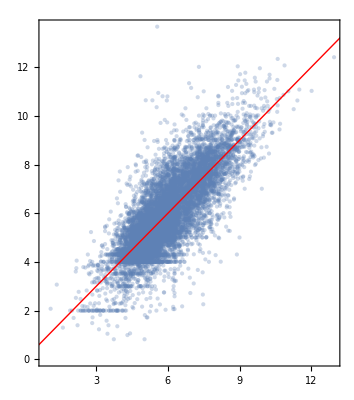

0.79562

```mathematica
Show[
ListPlot[Transpose[{xValues,yValues}],PlotStyle->{PointSize[Medium],Opacity[0.3]},PlotRange->All,AspectRatio->{1},Frame->True],
Plot[x,{x,-20,20},PlotStyle->{Red,Thick}],AspectRatio->{1}]

Correlation[xValues,yValues]
```

```mathematica
xValuesTrain=Flatten[Denormalize[#,scalingParams]&/@plapt[trainInputs]];
yValuesTrain=Denormalize[#,scalingParams]&/@trainOutputs;
```

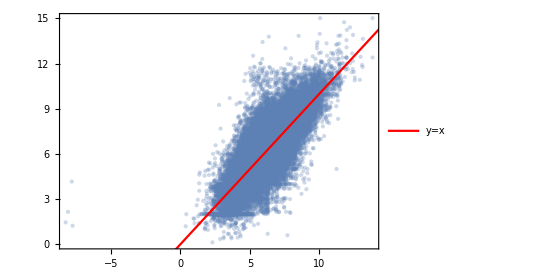

0.799263

```mathematica
Show[
ListPlot[Transpose[{xValuesTrain,yValuesTrain}],PlotStyle->{PointSize[Medium],Opacity[0.3]},PlotRange->All,AspectRatio->{1},Frame->True],
Plot[x,{x,-20,20},PlotStyle->{Red,Thick},PlotLegends->{"y=x","Best Fit Line"}],AspectRatio->{1}]

Correlation[xValuesTrain,yValuesTrain]
```

## Real World Example

```mathematica
testProtein=Entity["Protein","DEFB4"]
```

defensin, beta 4 precursor

```mathematica
ProteinData[testProtein,"MoleculePlot"]
```

-Graphics3D-

```mathematica
testProteinSequence=testProtein["Sequence"]
```

MRVLYLLFSFLFIFLMPLPGVFGGIGDPVTCLKSGAICHPVFCPRRYKQIGTCGLPGTKCCKKP

```mathematica
ProteinTokenizer[testProteinSequence]
```

{2,21,13,8,5,20,5,5,19,10,19,5,19,11,19,5,21,16,5,16,7,8,19,7,7,11,7,14,16,8,15,23,5,12,10,7,6,11,23,22,16,8,19,23,16,13,13,20,12,18,11,7,15,23,7,5,16,7,15,12,23,23,12,12,16,3}

```mathematica
testMolecule=Entity["Chemical","StearicAcid"];
```

```mathematica
MoleculePlot3D[testMolecule]
```

-Graphics3D-

```mathematica
testMoleculeSmiles=testMolecule["SMILES"]
```

CCCCCCCCCCCCCCCCCC(=O)O

```mathematica
MoleculeTokenizer[testMoleculeSmiles]
```

{0,693,285,365,263,51,13,51,2}

## Conclusion and Future Work

## Acknowledgements